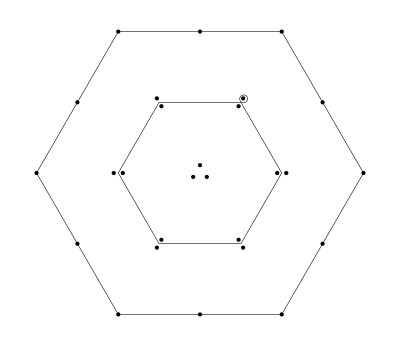

Y=1.5,  I_3=0.5

-(ud+du)(s̄d̄+d̄s̄)+(us+su)s̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C γ^μ u_b) ((d̄)_a γ^μ C((s̄)_b)^T-(d̄)_b γ^μ C((s̄)_a)^T)+(u_a^T C γ^μ d_b) ((d̄)_a γ^μ C((s̄)_b)^T-(d̄)_b γ^μ C((s̄)_a)^T)+(d_a^T C γ^μ u_b) ((s̄)_a γ^μ C((d̄)_b)^T-(s̄)_b γ^μ C((d̄)_a)^T)+(u_a^T C γ^μ d_b) ((s̄)_a γ^μ C((d̄)_b)^T-(s̄)_b γ^μ C((d̄)_a)^T)+((s̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((s̄)_b)^T) (s_a^T C γ^μ u_b)+((s̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((s̄)_b)^T) (u_a^T C γ^μ s_b)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-2 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 u)-2 (d̄(γ^μ).(γ̄)^5 u s̄(γ^μ).(γ̄)^5 d)+2 (d̄ γ^μ d s̄ γ^μ u)+2 (d̄ γ^μ u s̄ γ^μ d)+4 (s̄(γ̄)^5 s-d̄(γ̄)^5 d) (s̄(γ̄)^5 u)-4 (d̄(γ̄)^5 u s̄(γ̄)^5 d)+4 (d̄ 1d-s̄ 1s) (s̄ 1u)+4 (d̄ 1u s̄ 1d)+2 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 u)-2 (s̄ γ^μ s s̄ γ^μ u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(640 π^6)-(⟨ GG ⟩ log(-q^2/μ^2) q^4)/(32 π^5)+(⟨ ū u⟩ log(-q^2/μ^2) (2 m_d+m_s-3 m_u) q^4)/(12 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (2 m_d-m_s-m_u) q^4)/(6 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (2 m_d-3 m_s+m_u) q^4)/(12 π^4)-(8 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(10 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(576 π^6)+(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2-(4 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(2 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(6 π^2)+(⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(6 π^2)-(8 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(7 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(11 ⟨ s̄ Gs⟩^2)/(192 π^2 q^2)+(2 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)+(2 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)+(⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)-(11 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(96 π^2 q^2)-(11 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(96 π^2 q^2)-(11 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(192 π^2 q^2)-(16 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (m_d+2 m_s))/(9 q^2)-(16 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_u))/(9 q^2)+(64 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/(9 q^2)+(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (8 m_d+7 m_s+3 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩^3 (5 m_s+4 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (5 m_u-2 m_s))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

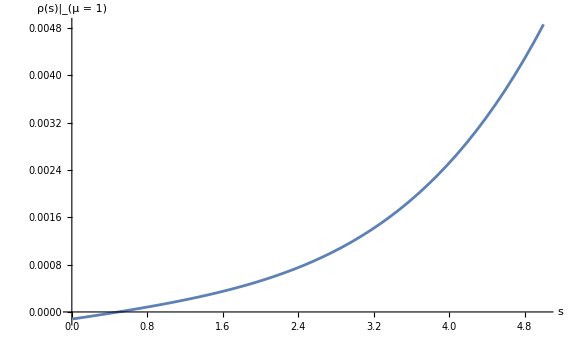
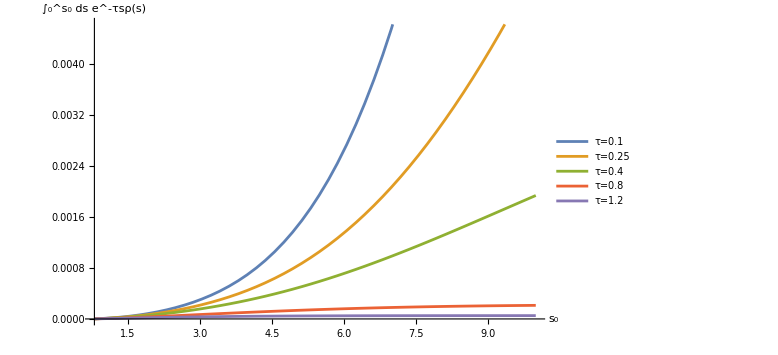

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

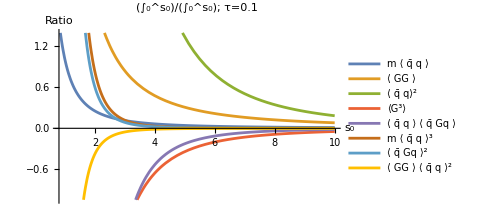
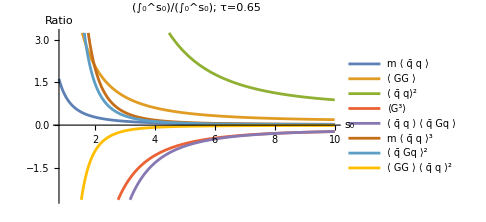
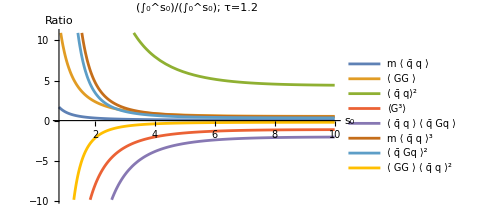

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

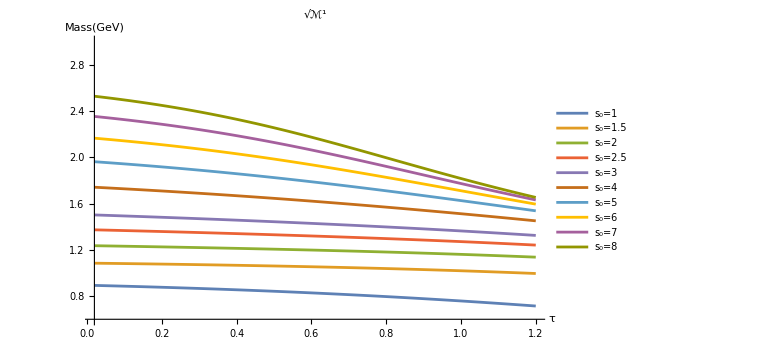
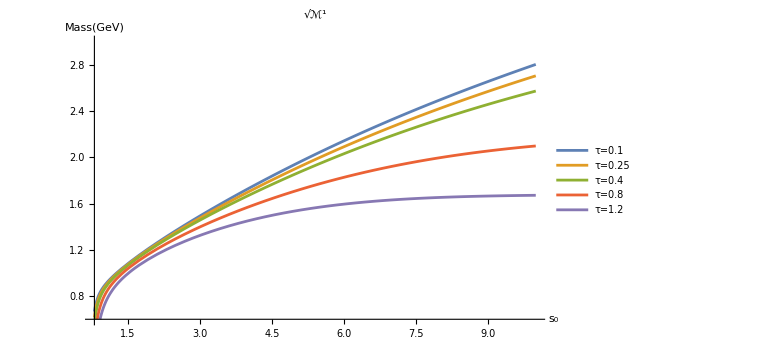

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

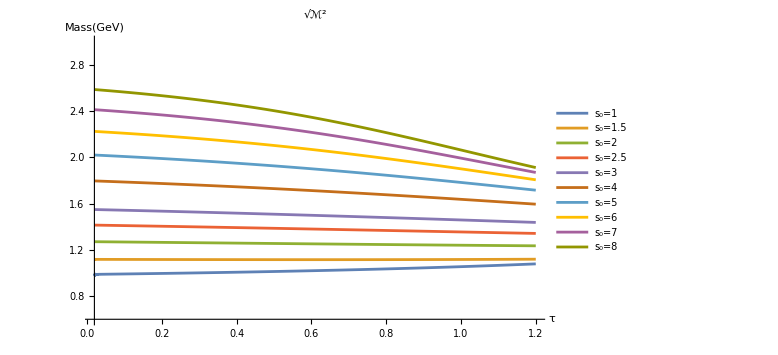
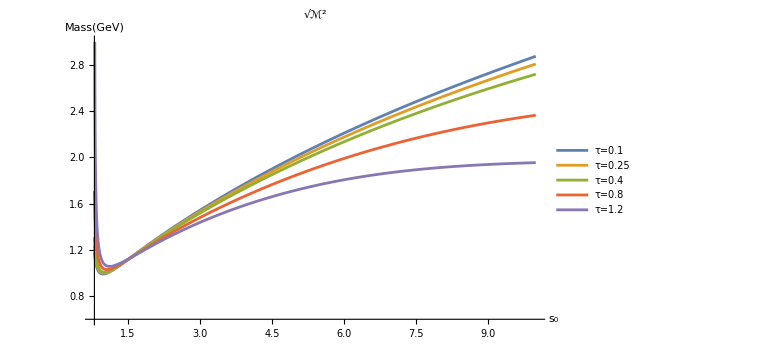

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

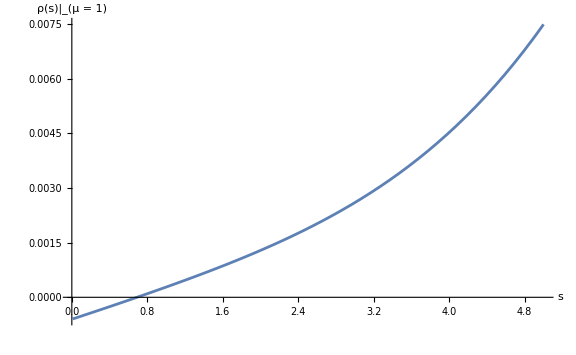
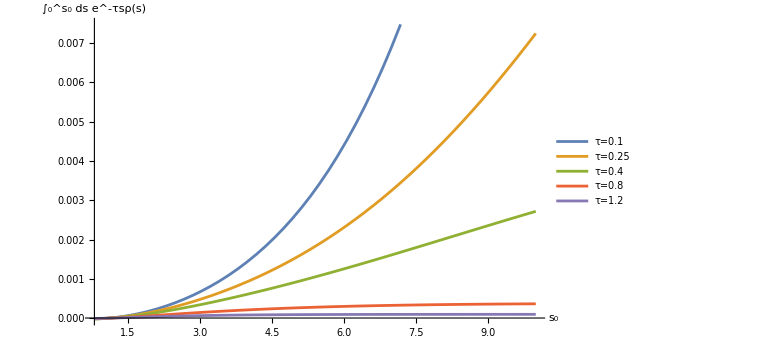

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

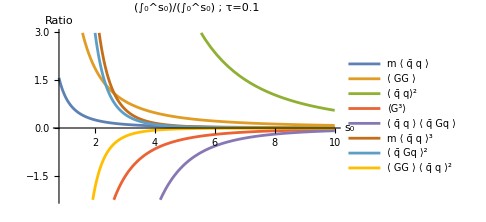
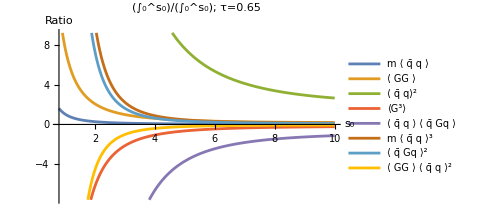
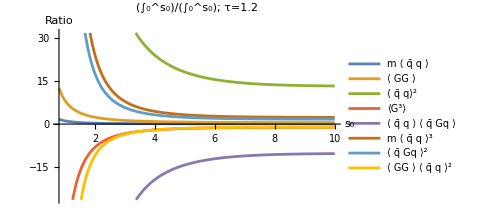

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

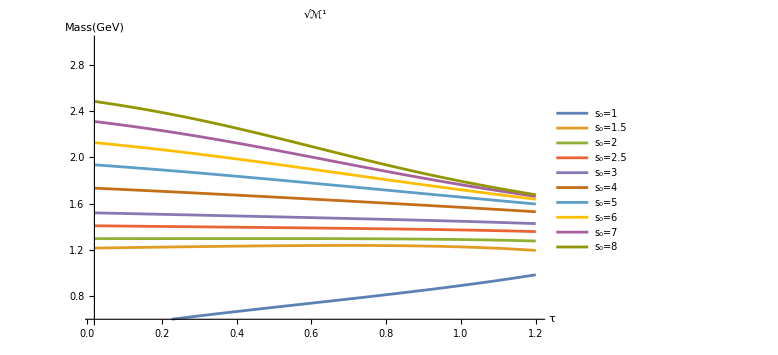
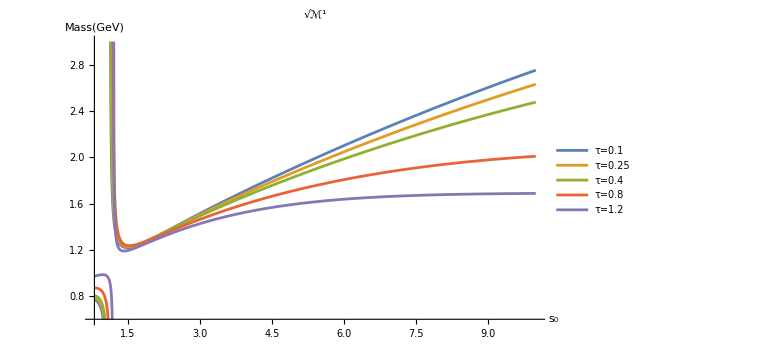

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5